## Brian — 2025-01-17 — PS 1— Solution

## Exercises from EIWL3 Section 1

```mathematica
1+2+3
```

6

```mathematica
1+2+3+4+5
```

15

```mathematica
1 2 3 4 5
```

120

```mathematica
5^2
```

25

```mathematica
3^4
```

81

```mathematica
10^12
```

1000000000000

```mathematica
3^(7 8)
```

523347633027360537213511521

Comment: The previous exercise was Ex. 1.7, and to solve it, I had to use parentheses, which had not been discussed. From this, we are put on warning that Wolfram will sometimes expect us to use things that he hasn’t explicitly introduced. The next exercise is Ex. 1.8, and in that one, he explicitly introduces parentheses. The point is that you sometimes have to look a little ahead to do the exercises.

```mathematica
(4-2)(3+4)
```

14

```mathematica
29000 73
```

2117000

## Exercises from EIWL3 Section 2

```mathematica
Plus[7,6,5]
```

18

```mathematica
Times[2,Plus[3,4]]
```

14

```mathematica
Max[Times[6,8],Times[5,9]]
```

48

```mathematica
RandomInteger[1000]
```

477

```mathematica
Plus[10,RandomInteger[10]]
```

17

## Exercises from EIWL3 Section 3

```mathematica
Range[4]
```

{1,2,3,4}

```mathematica
Range[100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
Reverse[Range[4]]
```

{4,3,2,1}

```mathematica
Reverse[Range[50]]
```

{50,49,48,47,46,45,44,43,42,41,40,39,38,37,36,35,34,33,32,31,30,29,28,27,26,25,24,23,22,21,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

```mathematica
Join[Range[4],Reverse[Range[4]]]
```

{1,2,3,4,4,3,2,1}

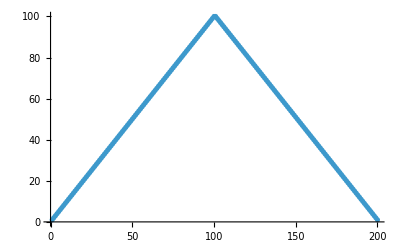

```mathematica
ListPlot[Join[Range[100],Reverse[Range[100]]]]
```

```mathematica
Range[RandomInteger[10]]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Range[10] (* Is a simpler expression for Reverse[Reverse[Range[10]]] *)
```

{1,2,3,4,5,6,7,8,9,10}

## Exercises from EIWL3 Section 4

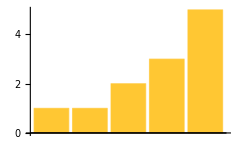

```mathematica
BarChart[{1,1,2,3,5}]
```

```mathematica
PieChart[Range[10]]
```

-Graphics-

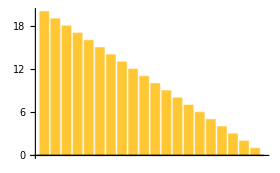

```mathematica
BarChart[Reverse[Range[20]]]
```

```mathematica
Column[Range[5]]
```

1
2
3
4
5

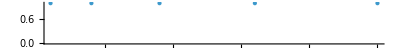

```mathematica
NumberLinePlot[Range[5]^2] (* You might be surprised that in my solution I "squared" a list.The key is that exponentiation is Listable,  meaning that it will exponentiate each element of a list when given a list. *)
```

```mathematica
Range[10]^2
```

{1,4,9,16,25,36,49,64,81,100}

Another way to make the same number line plot is:

```mathematica
NumberLinePlot[Power[Range[5],2]]
```

-Graphics-

```mathematica
PieChart[{1,1,1,1,1,1,1,1,1,1}]
```

-Graphics-

Comment: This is another one of those problems where Wolfram is thinking you might look ahead a little to come up with the solution. Specifically, in Section 6, he is going to introduce the Table function,  and the easiest application of Table is to make repeated numbers:

```mathematica
Table[1,10]
```

{1,1,1,1,1,1,1,1,1,1}

```mathematica
PieChart[Table[1,10]]
```

-Graphics-

```mathematica
Column[{
PieChart[Table[1,1]],
PieChart[Table[1,2]],
PieChart[Table[1,3]]
}]
```

-Graphics-